```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/Top-FormFactors-FA/Top-FormFactors-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g g → t t (Form Factors)

in total: 4 Particles insertions

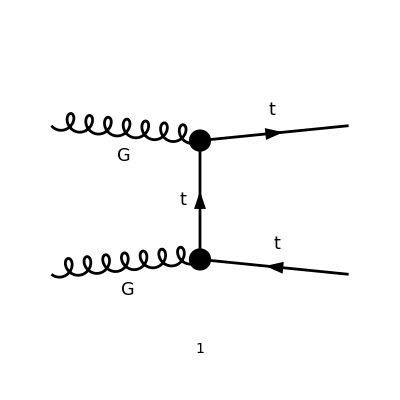

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =    { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[tops0,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]},GenericModel->"../../Models/Top-FormFactors-FA/Top-FormFactors-FA_FC"];
goodDiags=allDiags;
goodDiags=DiagramExtract[allDiags,{3}];
Paint[goodDiags,ColumnsXRows->{4,1},ImageSize->{ 800,200},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,TransversePolarizationVectors->{k1,k2},FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};

ampB =Simplify[SUNSimplify[DiracSimplify[ampA]]]
(* Remove terms of higher order *)
ampB = Normal[Series[ampB,{yDM,0,2},{gs,0,2}]];
```

in total: 1 Particles amplitude

-(ⅈ gs^2 (1373+1+2 1 (p2·ε(k2))) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)
 |  |  |  |

```mathematica
(* Fix Gauge and replace C00ren by the PV loop integrals and the counter-term *)
ampC =ampB/.{GaugeXi[V[Index[Generic,5]]]->1,C00ren->C00-MT^2 (C1+C11+C12)+(s/2)*(C11-C12)+deltaCTR};
```

```mathematica
(* Remove SM contribution *)
ampSM=gs^2 SeriesCoefficient[ampC,{gs,0,2},{yDM,0,0}];
ampC=Simplify[ampC-ampSM];
```

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,MT,MT,0,0];
```

```mathematica
ampEsimp=Simplify[DotSimplify[DiracSimplify[ampC]]];
ampEsimp2=DiracSimplify[ampEsimp/.{DiracGamma[7]->1-DiracGamma[6]}];
```

```mathematica
spinorChains=Sort[Tally[Cases[ampEsimp2,Spinor[___].___.Spinor[___],All]][[All,1]]]
pairs=Cases2[ampEsimp2,Pair]
gammas=Cases2[ampEsimp2,DiracGamma]
allTerms=Sort[Join[spinorChains,gammas]];
```

{(φ(p1,MT)).(φ(-p2,MT)),(φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(φ(-p2,MT)),(φ(p1,MT)).(γ·k1).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·k2).(γ·ε(k2)).(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·k1).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT))}

{k2·ε(k1),p1·ε(k1),p2·ε(k1),p2·ε(k2)}

{(γ̄)^6,γ·k1,γ·k2,γ·ε(k1),γ·ε(k2)}

### Coefficients for each term

```mathematica
Table[{allTerms[[i]],FullSimplify[Coefficient[ampEsimp2,allTerms[[i]]]]},{i,1,Length[allTerms]}]
```

((γ̄)^6 | 0
γ·k1 | 0
γ·k2 | 0
γ·ε(k1) | 0
γ·ε(k2) | 0
(φ(p1,MT)).(φ(-p2,MT)) | -(4 ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4 (k2·ε(k1)-p2·ε(k1)))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) | (4 ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4 (k2·ε(k1)-p1·ε(k1)-p2·ε(k1)))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(φ(-p2,MT)) | -(4 ⅈ π^2 gs^2 yDM^2 (p2·ε(k2)) (MT^2 (C1+C11+C12)+2 deltaCTL) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·k1).(γ̄)^6.(φ(-p2,MT)) | -(2 ⅈ π^2 gs^2 yDM^2 (C1+C11+C12) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4 (k2·ε(k1)-p1·ε(k1)-p2·ε(k1)))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·k2).(γ·ε(k2)).(φ(-p2,MT)) | (2 ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12) (T^Glu1 T^Glu2)_Col3Col4 (k2·ε(k1)-p2·ε(k1)))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) | -(ⅈ π^2 gs^2 yDM^2 (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4 (8 C00+C1 (-8 MT^2+s+7 t+u)+C11 (-8 MT^2+5 s+7 t+u)+C12 (-8 MT^2-3 s+7 t+u)-8 deltaCTL+8 deltaCTR))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(φ(-p2,MT)) | -(2 ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(φ(-p2,MT)) | (ⅈ π^2 gs^2 MT yDM^2 (T^Glu1 T^Glu2)_Col3Col4 (-2 C00-t (C1+C11+C12)+C1 MT^2+C11 MT^2-C11 s+C12 MT^2+C12 s+2 deltaCTL-2 deltaCTR))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) | -(2 ⅈ π^2 gs^2 yDM^2 (MT^2-t) (C1+C11+C12) (T^Glu1 T^Glu2)_Col3Col4 (k2·ε(k1)-p2·ε(k1)))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) | -(2 ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12) (T^Glu1 T^Glu2)_Col3Col4 (k2·ε(k1)-p1·ε(k1)-p2·ε(k1)))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(φ(-p2,MT)) | (4 ⅈ π^2 deltaCTL gs^2 yDM^2 (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) | (2 ⅈ π^2 gs^2 MT yDM^2 (T^Glu1 T^Glu2)_Col3Col4 (2 C00+C1 (t-MT^2)+C11 (-MT^2+s+t)-C12 (MT^2+s-t)-2 deltaCTL+2 deltaCTR))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·k1).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) | (ⅈ π^2 gs^2 yDM^2 (C1+C11+C12) (T^Glu1 T^Glu2)_Col3Col4 (k2·ε(k1)-p1·ε(k1)-p2·ε(k1)))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) | (ⅈ π^2 gs^2 yDM^2 (T^Glu1 T^Glu2)_Col3Col4 (8 C00+C1 (-6 MT^2+s+5 t+u)+C11 (-6 MT^2+5 (s+t)+u)+C12 (-6 MT^2-3 s+5 t+u)-8 deltaCTL+8 deltaCTR))/(2 ((k2-p2)^2-MT^2)))